## Shift + enter ready :)

a is your data for the bw chart...

```mathematica
a = {{1.2926067009237785,1.3743164625796276,1.1225121911022677,2.2876111220347783,1.6325164557613576,0.9449331437882094,0.9582397196759371,1.1874042180374376,2.367544447098543,2.0668413734288196,1.1949144638031834,0.8677633690778608,2.736724886769384,2.911414512635993,2.0774362897764784,0.9716249322686881,0.8587911620335632,1.1330034040671293,8.728784953718899,1.5783286692378204,1.122499186775184,7.575540331181907},{2.0430880115406937,2.1051229608986266,0.9327937261454182,1.0496735066000724,1.4211622842052876,0.9697888756813955,1.2166346523485643,0.9178830463365724,0.7346389903939429,1.1451571049328026,0.921254833768183,1.1526679692124282,1.7589750737543677,1.3225620236242062,0.978921157338498,1.7754287522547902,0.9051520460897626,0.9333157112879561},{0.826253519156344,0.8719936173753439,1.276123457789925,0.7922043433808952,0.8512996623463474,0.6718707619464881,0.9360432116898403,3.17323497360936,2.061060024690737,0.9457423013248138,0.8902191031189537,0.9133258480462167,0.5470992461059774,0.863304677963362,0.7162882522274562,1.141226654654452,0.8407045838907252,0.6470071541470541,0.7105764915600058,0.519447069974053,0.8679847577779861,1.1478045754416288,1.692016736651186,0.7440411570871714,0.9451904384799656,0.8466669279615315}};
```

```mathematica
x1line = Plot[x=1,{x,0,3.5}, PlotStyle->Opacity[0.2,Gray]];
```

Including vs excluding the outliers in the fences calculation:

Quartiles, 0-1                          Quartiles, -outliers                         Quartiles, 5% - 95%

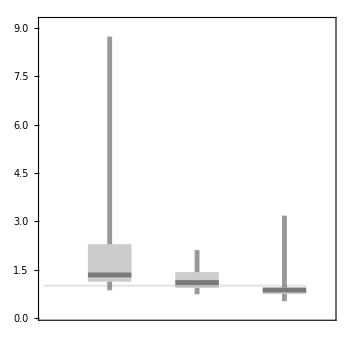
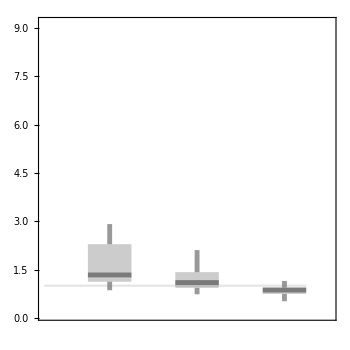
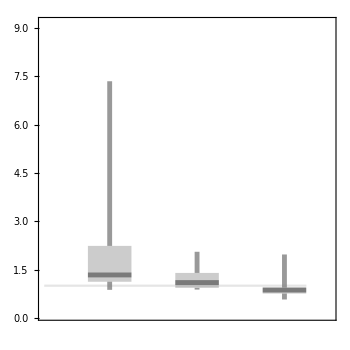

```mathematica
Row[{"        Quartiles, 0-1                          ", "Quartiles, -outliers                         ", "Quartiles, 5% - 95% "}]
Row[{
Show[  BoxWhiskerChart[a , {{"MedianMarker",Thickness[.01]},{"Whiskers",Thickness[.01]},{"Fences",.1,Opacity[0]}},ChartBaseStyle-> Directive[ Opacity[0.4,Gray]  ]  ] ,b,  Plot[x=1,{x,0,3.}, PlotStyle->Opacity[0.2,Gray] ], AspectRatio -> 1, ImageSize->350] ,

Show[  BoxWhiskerChart[a , {{"Outliers",""},{"FarOutliers",""},{"MedianMarker",Thickness[.01]},{"Whiskers",Thickness[.01]},{"Fences",.1,Opacity[0]}},ChartBaseStyle-> Directive[ Opacity[0.4,Gray]  ]  ] ,b,  Plot[x=1,{x,0,3.}, PlotStyle->Opacity[0.2,Gray] ], AspectRatio -> 1, ImageSize->350],

Show[  BoxWhiskerChart[a , {{"MedianMarker",Thickness[.01]},{"Whiskers",Thickness[.01]},{"Fences",.1,Opacity[0]}},Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)},ChartBaseStyle-> Directive[ Opacity[0.4,Gray]  ]  ] ,b,  Plot[x=1,{x,0,3.}, PlotStyle->Opacity[0.2,Gray] ], AspectRatio -> 1, ImageSize->350] 

}]
```

```mathematica
quantsa = Quantile[a[[1]],{0.05,0.25,0.5,0.75,0.95}]
```

{0.867763,1.1225,1.29261,2.28761,7.57554}

```mathematica
(*quants = {.025,.341,.5,.844,.975}
```

```mathematica
quants2={.5-.997/2,.5-.68/2,.5,.5+.68/2,.5+.997/2}
```

{0.0015,0.16,0.5,0.84,0.9985}

```mathematica
quants2
```

{0.0015,0.16,0.5,0.84,0.9985}

```mathematica
x1line
```

-Graphics-

```mathematica
test={Mean@#,StandardDeviation@#,Median@#}&/@a
```

{{2.13597,2.04943,1.33346},{1.23801,0.416204,1.09742},{1.01687,0.550014,0.865645}}

Make a random distribution to calculate your stdevs of data...

```mathematica
data=RandomVariate[#,100000]&/@(NormalDistribution[#⟦1⟧,#⟦2⟧]&/@test);
```

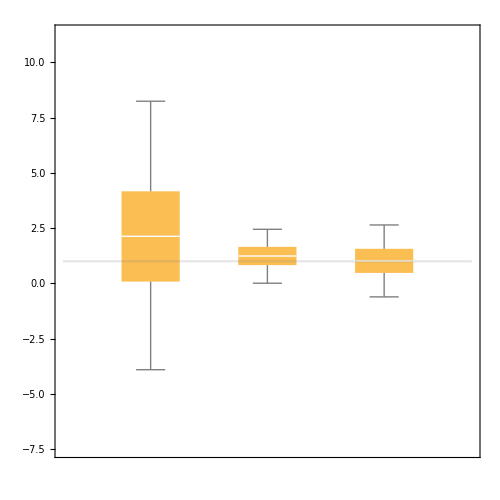
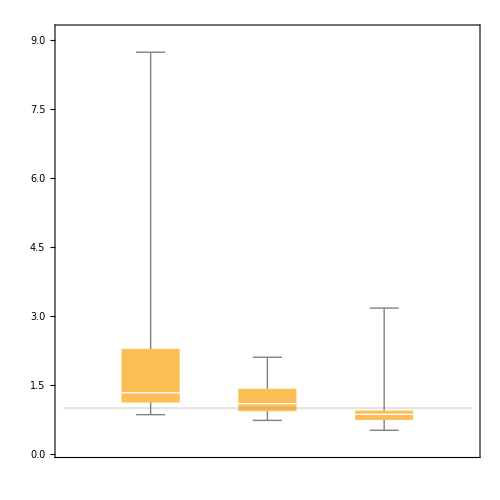
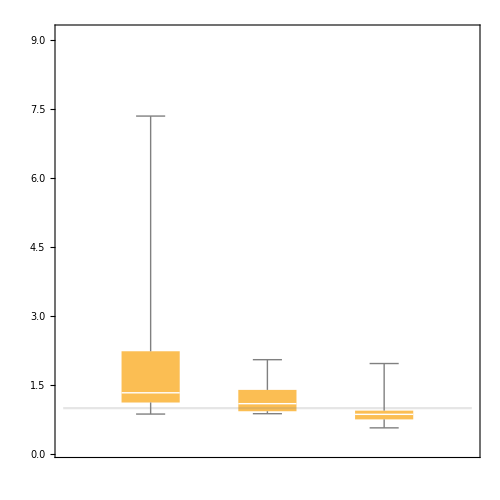

```mathematica
Row[{ 
Show[BoxWhiskerChart[data,Method->{"BoxRange"->(Quantile[#,quants2,{{1,-1},{0,1}}]&)} ],x1line, b,ImageSize->500 , AspectRatio->1,PlotRange-> {10,-5}],
Show[BoxWhiskerChart[a],  x1line,b,ImageSize->500 ,AspectRatio->1,PlotRange-> {10,-5}],

Show[BoxWhiskerChart[a,Method->{"BoxRange"->(Quantile[#,{0.05,0.25,0.5,0.75,0.95},{{1,-1},{0,1}}]&)} ],  x1line,b,ImageSize->500 ,AspectRatio->1,PlotRange-> {10,-5}]
}]
```